### 1. 求导

```mathematica
u = Function[x,x^2]
```

Function[x,x^2]

```mathematica
v = ((E^#) &)
```

ⅇ^#1&

```mathematica
v[x]
```

ⅇ^x

```mathematica
u[x]
```

x^2

```mathematica
w = Function[x,u[x] v[x]]
w[x]
```

Function[x,u[x] v[x]]

ⅇ^x x^2

```mathematica
Derivative[w[x]]
```

Derivative[ⅇ^x x^2]

```mathematica
w'[x]
```

2 ⅇ^x x+ⅇ^x x^2

```mathematica
u'[x]
```

2 x

```mathematica
v'[x]
```

ⅇ^x

```mathematica
v = Function[x, E^x]
```

Function[x,ⅇ^x]

```mathematica
v'[x]
```

ⅇ^x

```mathematica
Log[E]
```

1

```mathematica
N[Log[E]]
```

1.

```mathematica
N[E]
```

2.71828

### 2. 尝试求偏导数

```mathematica
x^2 + y^2 == 1
```

x^2+y^2==1

```mathematica
e1 = %
```

x^2+y^2==1

```mathematica
e1
```

x^2+y^2==1

```mathematica
e1'[x]
```

(x^2+y^2==1)'[x]

```mathematica
f2 = Function[{x, y}, x^2 + y^2]
```

Function[{x,y},x^2+y^2]

```mathematica
f2'[x]
```

Function[{x,y},x^2+y^2]'[x]

```mathematica
D[f2[x], x]
```

Function::fpct: Too many parameters in {x,y} to be filled from Function[{x,y},x^2+y^2][x].

Function::fpct: Too many parameters in {x,y} to be filled from Function[{x,y},0][x].

Function[{x,y},0][x]+Function[{x,y},x^2+y^2]'[x]

```mathematica
DSolve[2x+2y'[x]==0,y[x],x]
```

{{y[x]→-x^2/2+C[1]}}

```mathematica
Clear[{x,y}]
eq1 = E^(x+y)==x+y
```

ⅇ^(x+y)==x+y

```mathematica
dydx = DSolve[{Exp[x + y[x]]==x+y[x], y[0] == 0}, y'[x], x]
```

DSolve[{ⅇ^(x+y[x])==x+y[x],y[0]==0},y'[x],x]

```mathematica
DSolve[y'==y]
```

{{y→Function[{x},ⅇ^x C[1]]}}

### 3. 求x^2 + y^2 = 1的偏导数

```mathematica
eq2 = x^2 + y^2 == 1
```

x^2+y^2==1

```mathematica
D[x^2 + y[x]^2 == 1, x]
```

2 x+2 y[x] y'[x]==0

```mathematica
Solve[D[x^2 + y[x]^2 == 1, x], y'[x]]
```

{{y'[x]→-x/y[x]}}

```mathematica
ImplicitD[x^2 + y^2 == 1, x,y]
ImplicitD[x^2 + y^2 == 1, y, x]
```

-y/x

-x/y

### 使用隐函数求导练习

```mathematica
eq1 = E^(x+y)==x+y
```

ⅇ^(x+y)==x+y

```mathematica
ImplicitD[eq1, x, y]
ImplicitD[eq1, y, x]
```

-1

-1

```mathematica
eq2 = x == Cos[t]
eq3 = y == Sin[t]
```

x==Cos[t]

y==Sin[t]

```mathematica
deq2 = D[eq2, t]
deq3 = D[eq3, t]
```

0==-Sin[t]

0==Cos[t]

```mathematica
Solve[{deq2, deq3}, y'[t]]
```

{}

```mathematica
x[t_] := Cos[t]
y[t_] := Sin[t]
```

```mathematica
dxdt = D[x[t],t]
dydt = D[y[t],t]
dydx = dydt / dxdt
```

-Sin[t]

Cos[t]

-Cot[t]

```mathematica
Simplify[dydx]
```

-Cot[t]

```mathematica
eq1 = x^2 + y^2 == 1
eq2 = x * y == 2
```

x^2+y^2==1

x y==2

```mathematica
deq1 = D[eq1, x]
deq2 = D[eq2, x]
```

2 x==0

y==0

```mathematica
Solve[{deq1, deq2}, y'[x]]
```

{}

### 积分

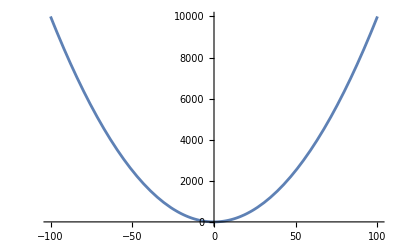

x^3/3

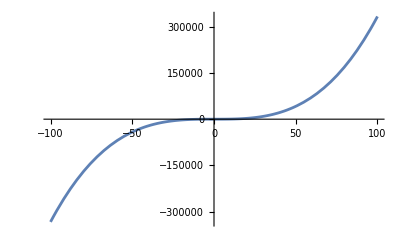

```mathematica
Plot[x^2, {x, -100, 100}]
f1 = Integrate[x^2,x]
Plot[f1,{x, -100,100}]
```

### 体会一下差别。注意，结果是一样的。

```mathematica
s1 = Sum[1/x^2,{x,1,10000000000000}];
s2 =N[s1]
s3 = N[Pi^2/6]
```

$Aborted

1.64393

1.64493

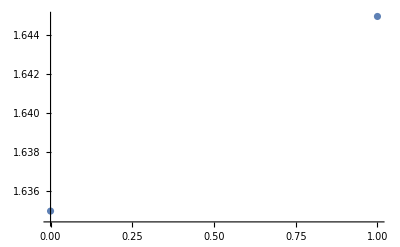

```mathematica
ListPlot[{{0,s2},{1, s3}}]
```

```mathematica
f2 = Function[1/x]
f2=1/#&
```

1/x&

1/#1&

```mathematica
Plot[f2, {x, -100,100}]
```

-Graphics-